## Epidemieausbreitung Europa

Victor Lachmann, 3034993
Henrik Spielvogel, 4013393

### Dieses Notebook wurde im Rahmen einer Projektarbeit des Moduls Computational Physics erstellt und behandelt die Modellierung einer Epidemie bezüglich des SIR-Modells und eines selbst erstellten Reise-Modells für Europa beziehungsweise Nordamerika. Aufgrund der großen Rechenzeit, die zum Erstellen der benötigten Listen erfordert ist, sollte dieses Notebook nicht mit der Funktion “Evaluate Notebook” an einem Stück ausgewertet werden. Stattdessen sollten zu Beginn nur die Initialisierungszellen ausgewertet werden. Alle weiteren Zellen, die manuell ausgewertet werden sollen, sind hellblau hinterlegt. Hellgrün hinterlegte Zellen sollten nicht ausgewertet werden, sie verdeutlichen nur die Vorgehensweise beim ersten Erstellen der verwendeten Listen. Diese Listen wurden zum Sparen von Rechenzeit bereits exportiert und werden nun bei jedem Start des Notebooks importiert.

## Erstellung aller benötigten Listen bzw. globalen Variablen

### Um ein geeignetes Netzwerk für Europa zu erstellen, werden einige Listen benötigt. Unser Modell beinhaltet alle Städte Europas mit mehr als 200.000 Einwohnern. Für das Reisemodell betrachten wir nur Land- und Luftverkehr und gehen wir davon aus, dass lediglich Städte mit mehr als 2.000.000 Einwohnern einen Flughafen besitzen. Um dies umzusetzen, werden folgende Listen erstellt:

Liste aller Städte mit Einwohnerzahl > 200.000

```mathematica
cities=Sort[Select[Flatten[  (*Liste wird alphabetisch sortiert und geflattet*)
CityData[{Large,#}]&/@ (*zuerst werden alle Städte Europas vorselektiert mit 'Large' - also alle Städte mit 100.000 und mehr Einwohner*)
(CountryData[#,"Name"]&/@ (*die Länder Entities von Europa werden zu Text umgewandelt, damit CityData damit arbeiten kann*)
CountryData["Europe"])],(*alle Länder Europas werden aufgelistet als Entities*)
Normal[CityData[#,"Population"]]>200000&]];(*alle Largen Städte Europas mit mehr als 200k Einwohner werden selektiert*)
```

Liste der Einwohnerzahl aller Städte

```mathematica
pop=CityData[#,"Population"]&/@cities; (*Liste für jede Population wird in 'pop' gespeichert (natürlich in der gleichen Reihenfolge, wie die Städte in 'cities aufgelistet sind'*)
```

Liste aller Großstädte mit Einwohnerzahl > 2.000.000

```mathematica
bigcities=Sort[Select[cities,
Normal[CityData[#,"Population"]]>2000000&]]; (*alle Großstädte d.h. Einwohnerzahl größer 2mio werden in 'bigcities' gespeichert*)
```

Liste aller Flugreiseziele

```mathematica
air=Table[
Sow[Select[bigcities,
GeoDistance[bigcities[[i]],#]>Quantity[0,"Meters"]&]],(*GeoDistance gibt alle Städte in der jeweiligen Liste aus, welche die entsprechende Bedingung erfüllen*)
(* da man von jeder Großstadt in jede andere Großstadt reisen kann, gibt es keine Obergrenze für die Entfernung, lediglich in ein und die selbe Stadt kann nicht geflogen werden, daher Distance > 0.*)
{i,6}];//Reap//Last; (*alle Flugziele für eine Großstadt werden in 'air' gespeichert*)
(*Sow,Reap, Last werden in allen Berechnungen lediglich zur Listmanipulation verwendet und habe keinen tieferen Grund für die Verwendung*)
```

Liste aller Landreiseziele

```mathematica
land=Table[Sow[GeoNearest[cities,cities[[i]], (*GeoNearest sorgt dafür, dass alle Städte in einem gewissen Umkreis einer Liste angezeigt werden*)
{All,Quantity[500000,"Meters"]}]],(*Da wir in unserem Modell sagen, Landverkehr lediglich zu Städten im Umkreis von 500km stattfindet, wurden die entsprechende Obergrenze gewählt*)
{i,Length[cities]}];//Reap//Last;
```

### Die obigen Listen bestehen aus Entities, welche neben dem Namen der Stadt auch viele weitere Informationen wie Einwohnerzahl oder Geographische Lage enthalten. Da der Umgang mit Entities in der Simulation allerdings unpraktisch ist, werden im Folgenden Listen erstellt, die nur die Namen der Städte enthalten:

Liste der Namen aller Flugreiseziele

```mathematica
airnames=Table[(*Entites der Luftverbindungen werden wieder zu Strings bzw. dem Namen der Stadt umgewandelt, da man teilweise damit effizienter arbeiten kann*)
Sow[Normal[CityData[#,"Name"]&/@air[[i]]]],{i,Length[air]}];//Reap//Last;
```

Liste der Namen aller Landreiseziele

```mathematica
landnames=Table[(*Entites der Landverbindungen werden wieder zu Strings bzw. dem Namen der Stadt umgewandelt, da man teilweise damit effizienter arbeiten kann*)
Sow[Normal[CityData[#,"Name"]&/@land[[i]]]],{i,Length[land]}];//Reap//Last;
```

Liste der Namen aller Großstädte

```mathematica
bigcitynames=CityData[#,"Name"]&/@bigcities;(*Entites der Großstädte werden wieder zu Strings bzw. dem Namen der Stadt umgewandelt, da man teilweise damit effizienter arbeiten kann*)
```

Liste der Namen aller Städte

```mathematica
citynames=CityData[#,"Name"]&/@cities;(*Entites der cities werden wieder zu Strings bzw. dem Namen der Stadt umgewandelt, da man teilweise damit effizienter arbeiten kann*)
```

## Import der Daten für Europa:

### Wie oben bereits erwähnt werden nun die benötigten Listen Importiert und an die jeweiligen Variablen übergeben.

```mathematica
SetDirectory[NotebookDirectory[]];
bigcities=ToExpression[Import["bigcities.txt"]];
bigcitynames=Flatten[Import["bigcitynames.txt","Data"]];

air=ToExpression[Import["air.txt"]];
cities=ToExpression[Import["cities.txt"]];
pop=Normal[ToExpression[Import["pop.txt"]]];
citynames=Import["citynames.txt","Data"];
landnames=ToExpression[Import["landnames.txt","Data"]];
airnames=ToExpression[Import["airnames.txt","Data"][[1]]];
```

## Reisemodell

### Das Reisemodell für diese Simulation ist stark vereinfacht und besteht nur aus Land- und Luftreisen. Luftreisen sind nur von Großstädten (Einwohnerzahl > 2*10^6) aus in andere Großstädte möglich, wohingegen Landreisen von allen Städten aus möglich sind. Jedoch ist zu beachten, dass die Bewohner einer Stadt nur in Städte in einem Umkreis von 500km reisen können. Die reisen finden in jedem Zeitschritt statt und erfolgen instantan. Pt ist die Vermischungsrate, also gibt dieser Parameter an, wie schnell sich die Bevölkerungsgruppen unter den Reisezielen durchmischen. Die travelCalc Funktion berechnet den Reisestrom einer Stadt für die drei Bevölkerungsgruppen (susceptible, infected und recovered), indem das Verhältnis der jeweiligen Gruppe zur Gesamtbevölkerung der Stadt betrachtet wird (p0/pop0). listDest ist dabei die Liste der möglichen Land- oder Luftverbindungen der Ausgangsstadt. Hat eine Stadt keine Möglichkeit, über Land zu reisen, so wird der Reisestrom durch eine If-Abfrage direkt auf 0 gesetzt. Ansonsten wird das Verhältnis (pN/popN) aller möglichen Zielstädte gemittelt und die Differenz mit dem der Ausgangsstadt gebildet. Diese Differenz wird dann noch mit der Reisewahrscheinlichkeit pt und der Gesamtbevölkerung pop0 der Ausgangsstadt multipliziert und ergibt somit den Reisestrom für diese Stadt.

```mathematica
travelCalc[listDest_]:=If[Length[listDest]==0,0,pt*pop0*(Sum[pN[k]/popN[k],{k,listDest}]/Length[listDest]-p0/pop0)];
```

## SIR - Modell Grundlagen

### Um einen Krankheitsverlauf vereinfacht zu simulieren, wird die Bevölkerung in drei Gruppen aufgeteilt. Susceptible bezeichnet die Personen, die noch nicht infiziert wurden, es aber noch werden können. Infected beinhaltet die infizierten Personen und Recovered die bereits genesenen. Dabei wird angenommen, dass eine Person als susceptible geboren wird, nach der Infektion in die Gruppe infected gerät und nach Genesung in der Gruppe recovered verweilt. Außerdem soll die Gesamtbevölkerung konstant bleiben. In diesem Modell ist es nicht möglich, nach der Genesung erneut angesteckt zu werden, wie es beispielsweise bei Windpocken der Fall ist. Dadurch "rottet" sich eine Krankheit selbst aus, da nach einer gewissen Zeit keine infizierbaren Personen mehr in der Gruppe susceptible sind (ausgenommen Neugeborene). In den folgenden Modulen wird die zeitliche Entwicklung der Krankheit nach dem SIR-Modell berechnet. Dieses beruht auf einem System von Differentialgleichungen,welches die Änderung der Populationsgruppen (susceptible, infected, recovered) anhand der gegebenen Parameter β, ν und μ beschreibt. dS/dt=μ N-(β S I)/N-μ S dI/dt=(β S I)/N-ν I-μ I dR/dt=ν I-μ R β bezeichnet die Infektionsrate der Krankheit, also die Rate, mit der Personen von der Susceptible Gruppe in die Infected Gruppe übergehen. ν ist die Genesungsrate, die angibt, wie schnell Pesonen aus der Infected Gruppe in die Recovered Gruppe kommen. μ ist die Reproduktion- und Sterberate, somit die Rate , mit der Menschen von allen drei Gruppen in die Susceptible Gruppe übergehen. Um die Bedeutung der Parameter besser zu verstehen, haben wir ein Modul geschrieben, durch das die Auswirkung der Änderung der Parameter live dargestellt wird:

```mathematica
(*Hier habe ich eine neue Funktion für das Erstellen eines Manipulate erstellt, damit ich dieser Funtktion β und ν übergeben kann*)
infectNDSManipulate[j_,d_,β_,ν_,p_]:=Module[{μ,popN,s,i,r,sol,system,t}, 
popN=Normal[pop[[j]]];
μ=3*10^-5 ;(* es macht keinen Sinn μ zu variieren, da dieses nicht von der Krankheit, sondern von der Demographie abhängt*)

system={s'[t]==- β*s[t] i[t]/popN+popN*μ-μ*s[t],
i'[t]==β*s[t] i[t]/popN-ν*i[t]-μ*i[t],
r'[t]==ν* i[t]-μ*r[t],
s[0]==popN*(1-p),i[0]==popN*p,r[0]==0}; (* Es wird das gewohnte System an DGLs erstellt*)

sol=NDSolve[system,{s,i,r},{t,0,d}]; (* Das DGL System wird mittels NDSolve gelöst*)

Return[NDSolveValue[system,{s[d],i[d],r[d]},{t,d-1,d+1}]]] (* Es werden die entsprechenden Werte nach d Tagen von S,I und R als Vektor returned*)
Manipulate[ListLinePlot[{

Table[infectNDSManipulate[j,d,β,ν,p][[1]],{d,0,100}], (* Nach 100 Tagen sieht man spätestens bei jeder Stadt den charakteristischen Verlauf*)
Table[infectNDSManipulate[j,d,β,ν,p][[2]],{d,0,100}],
Table[infectNDSManipulate[j,d,β,ν,p][[3]],{d,0,100}]},
PlotLegends->{"Susceptible","Infected","Recovered"},PlotStyle->{Blue,Red,Green},AxesLabel->{"Tage","Personen"}],
{{β,0.46,"Ansteckungsparameter"},0,10,Appearance->"Open"}, (*β∈[0,10]*)
{{ν,0.126,"Genesungsparameter"},0,10,Appearance->"Open"}, (*ν∈[0,10]*)
{{j,29,"Index der Stadt"},1,Length[cities],1,Appearance->"Open"}, (*j∈[1,243](Anzahl der Städte)*)
{{p,0.042,"Anteil der Infizierten bei t = 0"},0,1,Appearance->"Open"}(*p∈[0,1](da s[0]==pop[[j]]*(1-p) und i[0]==pop[[j]]*p in NDSolve*)]
```

## Festlegen der Parameter und Erstellen grundlegender Funktionen/Listen

### Hier werden zunächst die Reiseparameter ptland und ptair festgelegt, welche dem oben erklärten Parameter pt entsprechen, jedoch aufgeteilt auf den Land- und Luftverkehr, sodass man diese getrennt voneinander variieren kann. Außerdem werden die für das SIR-Modell benötigten Parameter β (Ansteckungsparameter der Krankheit), ν (Genesungsparameter der Krankheit) und μ (Reproduktions- und Sterberate) festgelegt. Des Weiteren werden die Funktionen index und indexAir erstellt, die, wenn sie den Namen einer Stadt übergeben bekommen, die Position der Stadt in der jeweiligen Liste ausgeben. Die Listen indexLandList und indexAirList entsprechen den Listen land und air, nur dass statt der Stadt selbst der Index dieser in der Liste steht. Die infect Funktion dient zur Initialisierung der Simulation. Ihr sind eine Ausgangsstadt und die Anzahl der dort zu infizierenden Personen zu übergeben.

```mathematica
ptland=0.01;
ptair=0.01;

beta=0.1;
nu=0.07;
mu=3*10^-5;

index[city_String]:=Position[citynames,city]⟦1,1⟧;
indexAir[city_String]:=Position[bigcitynames,city][[1,1]];
indexLandList=Map[index[#]&,landnames,{2}];
indexAirList=Map[index[#]&,airnames,{2}];



infect[city_,inf0_]:=Module[{j,inf1,landinf1},
j=index[city];

(*Erstellen einer Liste der infizierten Personen pro Stadt. Nur in der Stadt "city_" werden "inf0_" Personen infiziert.*)
inf1={Table[If[j==i,inf0,0],{i,Length[cities]}]};     

(*Die Anzahl der noch infizierbaren Personen ergibt sich aus der Differenz der Gesamtbevölkerung einer Stadt und den darin infizierten Personen*)
sus={pop}-inf1;

inf=inf1;

(*Zu Begin der Simulation gibt es noch keine genesenen Personen*)
rec={Table[0,Length[cities]]};
]

citiesPos=Map[GeoPosition[#]&,cities,{1}]; (*Erstellen einer Liste mit den Koordinaten der einzelnen Städte für die spätere Animation*)
```

## Reisefunktionen für eine einzelne Stadt

### travelLand und travelAir wenden jeweils die travelCalc Funktion auf die gewünschten Zielstädte aus der Liste listDest an und berechnen so die Änderung der Bevölkerung in der übergebenen Stadt “city_” . s0, i0 und r0 sind die Startwerte der drei Bevölkerungsgruppen, die dem letzten Element (also dem zuletzt durchgeführten Zeitschritt) der entsprechenden Liste entnommen werden. popNew ist eine dreielementige Liste, die dann der Bevölkerung der Stadt “city_” nach dem Zeitschritt entspricht (aufgeteilt in {sus,inf,rec}). Die beiden Module funktionieren im Grunde völlig analog zueinander, nur dass bei der travelAir Funktion ausschließlich die Städte mit Flughafen (d.h. Einwohnerzahl > 2+*10^6) berücksichtigt werden.

```mathematica
travelLand[city_]:=Module[{j,listDest,popChange,s0,i0,r0,popNew},
(*Erstellung der Zielliste listDest für die übergebene Stadt*)
j=index[city];
listDest=indexLandList[[j]];

(*Berechnung der Änderung der Bevölkerung *)
popChange=travelCalc[listDest];

(*Festlegen der Startwerte*)
s0=Last[sus][[j]];
i0=Last[inf][[j]];
r0=Last[rec][[j]];

(*Durch Ersetzungsregeln kann mit nur einer Funktion travelCalc direkt der neue Wert für die drei Bevölkerungsgruppen berechnet werden.*)
popNew=
{s0+popChange/.{p0->s0,pN[k_]:>Last[sus][[k]]},
i0+popChange/.{p0->i0,pN[k_]:>Last[inf][[k]]},
r0+popChange/.{p0->r0,pN[k_]:>Last[rec][[k]]}}
/.{pop0->s0+i0+r0,popN[k_]:>Last[sus][[k]]+Last[inf][[k]]+Last[rec][[k]],pt->ptland};
Return[popNew]
]

(*Durch die If-Abfrage wird das Modul nur dann aufgerufen, wenn es sich um eine Stadt mit Flughafen handelt.*)
travelAir[city_]:=If[MemberQ[bigcitynames,city],Module[{j,i,listDest,popChange,s0,i0,r0,popNew},
j=index[city];
i=indexAir[city];

listDest=indexAirList[[i]];

popChange=travelCalc[listDest];

s0=Last[sus][[j]];
i0=Last[inf][[j]];
r0=Last[rec][[j]];

popNew=
{s0+popChange/.{p0->s0,pN[k_]:>Last[sus][[k]]},
i0+popChange/.{p0->i0,pN[k_]:>Last[inf][[k]]},
r0+popChange/.{p0->r0,pN[k_]:>Last[rec][[k]]}}
/.{pop0->s0+i0+r0,popN[k_]:>Last[sus][[k]]+Last[inf][[k]]+Last[rec][[k]],pt->ptair};

Return[popNew]
],{Last[sus][[index[city]]],Last[inf][[index[city]]],Last[rec][[index[city]]]}]
(*Handelt es sich nicht um eine Stadt mit Flughafen, so wird lediglich der letzte Wert der Bevölkerung ausgegeben*)
```

## Reisefunktionen für alle Städte

### Um den Reiseverkehr auf dem gesamten Netzwerk zu simulieren, wenden die Funktionen travelLandAll und travelAirAll die obigen travel-Funktionen auf alle Städte an. Nach jedem Zeitschritt wird die neue Bevölkerungszahl der jeweiligen Gruppe an die entsprechende Liste angehängt. Somit erhält man mit jedem Zeitschritt ein neues Element, auf das im nächsten Zeitschritt mit der Last[] Funktion zugegriffen werden kann.

```mathematica
travelLandAll:=Module[{susN,infN,recN},
susN=Map[travelLand[#][[1]]&,citynames,{1}];
infN=Map[travelLand[#][[2]]&,citynames,{1}];       (*Anwenden der travel-Funktionen auf jede Stadt*)
recN=Map[travelLand[#][[3]]&,citynames,{1}];

AppendTo[sus,susN];
AppendTo[inf,infN];      (*Anhängen der neuen Listen an die Bestehenden*)
AppendTo[rec,recN];
]

travelAirAll:=Module[{susN,infN,recN},
susN=Map[travelAir[#][[1]]&,citynames,{1}];
infN=Map[travelAir[#][[2]]&,citynames,{1}];
recN=Map[travelAir[#][[3]]&,citynames,{1}];
AppendTo[sus,susN];
AppendTo[inf,infN];
AppendTo[rec,recN];
]
```

## SIR - Modell für eine einzelne Stadt

### Jedes der drei infect - Module bekommt eine Stadt übergeben, für welche es die Differentialgleichungen des SIR-Modells mit einer anderen Methode löst. infectNDS verwendet das in Mathematica integrierte NDSolve, infectEul das Euler - Verfahren und infectRK4 das Runge - Kutta - Verfahren 4. Ordnung. Beim Euler-Verfahren betrachtet man ein Anfangswertproblem der Form: dy/dt=f(t,y) , y(0)=y0 Zur Lösung dieses Problems diskretisiert man das Lösungsintervall und berechnet die Funktionwerte rekursiv, indem man auf den k-ten Funktionswert die Steigung am Punkt k, multipliziert mit der Schrittweite h, addiert.: y(k+1) = y(k) + h * f(t,y(k)) Das Runge-Kutta-Verfahren basiert auf dem selben Prinzip wie das Euler-Verfahren, jedoch werden in jedem Schritt 4 verschiedene Differenzenquotienten betrachtet, was die Fehler des Verfahrens gegenüber Euler verringert.

```mathematica
infectNDS[city_]:=Module[{j,sys,s,i,r,p,t,sN,iN,rN,sol,p0,i0,s0,r0},
j=index[city];

p0=pop[[j]];
i0=Last[inf][[j]];
s0=Last[sus][[j]];          (*Festlegen der Startwerte*)
r0=Last[rec][[j]];

sys={                         (*Erstellung des DGL-Systems nach dem SIR-Modell*)
s'[t]==mu*p0-beta*s[t]*i[t]/p0-mu*s[t],        
i'[t]==beta*s[t]*i[t]/p0-nu*i[t]-mu*i[t],
r'[t]==nu*i[t]-mu*r[t],

i[0]==i0,
s[0]==s0,        (*Einsetzen der Anfangswerte*)
r[0]==r0
};
sol=NDSolve[sys,{s[t],i[t],r[t]},{t,0,1}];     (*Lösung des Anfangswertproblems durch NDSolve*)
sN[t]=s[t]/.sol;
iN[t]=i[t]/.sol;             (*Anwendung der Lösung auf die jeweilige Funktion*)
rN[t]=r[t]/.sol;

Return[Flatten[{sN[t],iN[t],rN[t]}/.t->1]]              (*Ausgabe der Bevölkerungszahlen bei t=1*)
]

infectEul[city_]:=Module[{j,p0,i0,s0,r0,fs,fi,fr,fp,s,i,r,p,deltat,steps,val,k},
j=index[city];

p0=pop[[j]];
i0=Last[inf][[j]];
s0=Last[sus][[j]]; (*Festlegen der Startwerte*)
r0=Last[rec][[j]];

fs[p_,s_,i_]:=mu*p-beta*s*i/p-mu*s;
fi[s_,i_,p_]:=beta*s*i/p-nu*i-mu*i;   (*Steigungen der Funktionen*)
fr[i_,r_]:=nu*i-mu*r;
fp[]:=0;

deltat=1;
steps=1;           (*Schrittweite und Lösungsintervall*)

val=Drop[RecurrenceTable[{
s[k+1]==s[k]+deltat*fs[p[k],s[k],i[k]],
i[k+1]==i[k]+deltat*fi[s[k],i[k],p[k]],                 (*Iterative Berechnung der Funktionswerte*)
r[k+1]==r[k]+deltat*fr[i[k],r[k]],
p[k+1]==p[k],
s[0]==s0,i[0]==i0,r[0]==r0,p[0]==p0},{s,i,r,p},{k,0,steps}][[2]],{4,4}]

]

infectRK4[city_]:=Module[{j,i0,s0,r0,p0,sys,s,i,r,K1,K2,K3,K4,t,sol},
j=index[city];

p0=pop[[j]];
i0=Last[inf][[j]];
s0=Last[sus][[j]];   (*Festlegen der Startwerte*)
r0=Last[rec][[j]];

sys={s'[t]==mu*p0-beta*s[t]*i[t]/p0-mu*s[t],     (*Definition des DGL-Systems*)
i'[t]==beta*s[t]*i[t]/p0-nu*i[t]-mu*i[t],
r'[t]==nu*i[t]-mu*r[t]};

K1[y_]:=K1[y]=sys[[y,2]]/.{s[t]->s0,i[t]->i0,r[t]->r0};
K2[y_]:=K2[y]=sys[[y,2]]/.{s[t]->s0+K1[1]/2,i[t]->i0+K1[2]/2,r[t]->r0+K1[3]/2};
K3[y_]:=K3[y]=sys[[y,2]]/.{s[t]->s0+K2[1]/2,i[t]->i0+K2[2]/2,r[t]->r0+K2[3]/2};              (*Berechnung der Differenzenquotienten*)
K4[y_]:=K4[y]=sys[[y,2]]/.{s[t]->s0+K3[1],i[t]->i0+K3[2],r[t]-> r0+K3[3]};

sol={s0 +1/6 (K1[1]+2K2[1]+2K3[1]+K4[1]),
i0 +1/6(K1[2]+2K2[2]+2K3[2]+K4[2]),                (*Iteration des Funktionswertes durch anteilige Addition der Differenzenquotienten auf den vorherigen Funktionswert*)
r0 +1/6(K1[3]+2K2[3]+2K3[3]+K4[3])};
Return[sol]
]
```

## SIR-Modell übertragen auf alle Städte

### Analog zum Reisemodell wird hier die jeweilige infect-Funktion auf alle Städte angewendet und die daraus resultierende Liste der Bevölkerungsgruppe erneut an die bereits bestehende Liste angehängt. Dieses Vorgehen ist für alle infect-Funktionen gleich.

```mathematica
infectNDSAll:=Module[{susN,infN,recN,susO,infO,recO,landsusN,landinfN,landrecN,landpopN},
susN=Table[infectNDS[citynames[[i]]][[1]],{i,1,Length[cities]}];
infN=Table[infectNDS[citynames[[i]]][[2]],{i,1,Length[cities]}];          
recN=Table[infectNDS[citynames[[i]]][[3]],{i,1,Length[cities]}];
(*Anwenden der infect Funktion auf alle Städte und Erstellung einer Tabelle der neuen Bevölkerungswerte*)

AppendTo[sus,susN];
AppendTo[inf,infN];    (*Anhängen der oben erstellten Tabellen an die jeweiligen Listen*)
AppendTo[rec,recN];
]

infectEulAll:=Module[{susN,infN,recN,susO,infO,recO,landsusN,landinfN,landrecN,landpopN},
susN=Table[infectEul[citynames[[i]]][[1]],{i,1,Length[cities]}];
infN=Table[infectEul[citynames[[i]]][[2]],{i,1,Length[cities]}];
recN=Table[infectEul[citynames[[i]]][[3]],{i,1,Length[cities]}];
AppendTo[sus,susN];
AppendTo[inf,infN];
AppendTo[rec,recN];
]

infectRK4All:=Module[{susN,infN,recN,susO,infO,recO,landsusN,landinfN,landrecN,landpopN},
susN=Table[infectRK4[citynames[[i]]][[1]],{i,1,Length[cities]}];
infN=Table[infectRK4[citynames[[i]]][[2]],{i,1,Length[cities]}];
recN=Table[infectRK4[citynames[[i]]][[3]],{i,1,Length[cities]}];
AppendTo[sus,susN];
AppendTo[inf,infN];
AppendTo[rec,recN];
]
```

## Funktionen zum Ausführen der Zeitschritte

### doTimestep bekommt eine Ausgangsstadt “city_” als String, die Zahl der Infizierten “inf0_” bei t = 0 in dieser Stadt, die Anzahl der auszuführenden Zeitschritte “t_” und die gewünschte Lösungsmethode “Method_” der DGL übergeben (hier sind nur die Werte “NDS”, “Eul” und “RK4” zulässig). Beim Ausführen der Funktion wird die Simulation zunächst mit der infect Funktion initialisiert und daraufhin durch eine Do-Schleife sukzessive travelLandAll, travelAirAll und die jeweilige infect___All Funktion t_ mal ausgeführt. Da in jedem Zeitschritt jede Funktion (travelLandAll, travelAirAll, infect___All) jeweils eine Liste an die bestehenden sus, inf und rec Listen anhängt, beträgt die Länge dieser Listen nach t-maligem Ausführen der Do-Schleife 3*t.

```mathematica
doTimestep[city_,inf0_,t_,Method_]:=Module[{func},
infect[city,inf0]; (*Initialisierung der Simulation durch Infektion von inf0_ Personen in der Stadt city_*)

func:=Switch[Method,"RK4",infectRK4All,"Eul",infectEulAll,"NDS",infectNDSAll];    (*Auswahl der gewünschten Lösungsmethode*)
Do[
travelLandAll;     (*t_-maliges Ausführen der Reise- und Infect-Funktionen*)
travelAirAll;
func,t]
]
```

### Möchte man weitere Zeitschritte durchführen, die Simulation aber nicht von vorne beginnen lassen, so kann man dies mit der continueTimestep Funktion machen, indem man ihr die gewünschte Anzahl “t_” an Zeitschritten übergibt. Der einzige Unterschied zu doTimestep ist, dass die Simulation nicht erneut durch infect initialisiert wird. Somit nimmt die continueTimestep-Funktion die bereits erstellten Listen auf und hängt an diese an.

```mathematica
continueTimestep[t_,Method_]:=Module[{func},
func:=Switch[Method,"RK4",infectRK4All,"Eul",infectEulAll,"NDS",infectNDSAll];
Do[
travelLandAll;
travelAirAll;
func,t]
]
```

## Funktionen zum Plotten der SIR-Populationen

### Möchte man sich die Entwicklung der Bevölkerung anhand des SIR-Modells in einer Stadt graphisch anzeigen lassen, so muss man nur die gewünschte Stadt der plot-Funktion übergeben. Dabei werden die susceptible-, infected-, und recovered-Gruppen in Blau, Rot und Grün angezeigt.

```mathematica
plot[city_]:=Module[{j,susTable,infTable,recTable,susPlot,infPlot,recPlot},
j=indexGlobal[city];     

susTable=Table[sus[[i,j]],{i,1,Length[inf],3}];
infTable=Table[inf[[i,j]],{i,1,Length[inf],3}];    
recTable=Table[rec[[i,j]],{i,1,Length[inf],3}];
(*Erstellen von Listen mit der Zeitentwicklung der Bevölkerungszahlen der jeweiligen Gruppe für die Stadt city_ *)
(*Da in jedem Zeitschritt drei Listen angehängt werden, wird nur jeder 3. Eintrag aus sus, inf oder rec betrachtet.*)

ListLinePlot[{susTable,infTable,recTable},PlotStyle->{Blue,Red,Green},PlotLegends->{"susceptible","infected","recovered"},PlotLabel->StringJoin["Krankheitsverlauf in ",ToString[city]],AxesLabel->{"Zeit","Bevölkerung"}]
(*Erstellen eines Plots mit der Bevölkerungszahl auf der y-Achse und den Zeitschritten auf der x-Achse*)
]
```

### Um die Städte besser miteinander vergleichen zu können, wird bei der Funktion plotScaled nicht der Absolutbetrag der Bevölkerungsgruppen angezeigt, sondern nur der Anteil jeder Gruppe an der Gesamtbevölkerung der Stadt. Die Funktionsweise ist die Gleiche wie bei der plot-Funktion, nur dass hier die Einträge der sus- inf- und recTable auf die Gesamtbevölkerung der jeweiligen Stadt normiert sind.

```mathematica
plotScaled[city_]:=Module[{j,susTable,infTable,recTable,susPlot,infPlot,recPlot},
j=index[city];
susTable=Table[sus[[i,j]]/pop[[j]],{i,1,Length[inf],3}];
infTable=Table[inf[[i,j]]/pop[[j]],{i,1,Length[inf],3}];
recTable=Table[rec[[i,j]]/pop[[j]],{i,1,Length[inf],3}];

ListLinePlot[{susTable,infTable,recTable},{PlotStyle->{Blue,Red,Green},PlotLegends->{"susceptible","infected","recovered"},PlotLabel->StringJoin["Krankheitsverlauf in ",ToString[city]],AxesLabel->{"Zeit","relative Bevölkerung"}}]
]
```

### Die Funktion “plotScaledNoLabels” ist im Grunde die Selbe wie “plotScaled”, nur dass sie Keine Beschriftungen an die Plots anfügt. Dies ist nur notwendig, wenn man alle Plots übereinander legen möchte (so wie es im nächsten Modul “plotAll” der Fall ist), da ansonsten zu viele PlotLegends und Labels angezeigt werden und der Output dadurch sehr unübersichtlich wird.

```mathematica
plotScaledNoLabels[city_]:=Module[{j,susTable,infTable,recTable,susPlot,infPlot,recPlot},
j=index[city];
susTable=Table[sus[[i,j]]/pop[[j]],{i,1,Length[inf],3}];
infTable=Table[inf[[i,j]]/pop[[j]],{i,1,Length[inf],3}];
recTable=Table[rec[[i,j]]/pop[[j]],{i,1,Length[inf],3}];

ListLinePlot[{susTable,infTable,recTable},{PlotLabel->None,PlotStyle->{Blue,Red,Green}}]
]
```

### Nun kann man die skalierten Plots aller Städte übereinander legen und so einen Eindruck für die verspätete Infektion in anderen Städten durch die Reisedauer erlangen. Dies ist daran zu erkennen, dass einige der roten Kurven der Infizierten erst spät anfangen, anzusteigen und somit der ganze SIR-Prozess verspätet beginnt. Außerdem kann man immer eine Konstante sus-Linie bei 1 erkennen, was darauf zurückzuführen ist, dass die Stadt Nikosia auf Zypern keinerlei Reiseziele im Umkreis von 500km hat.

```mathematica
plotAll:=Module[{},
Show[Table[plotScaledNoLabels[citynames[[i]]],{i,Length[citynames]}]]
]
```

## Animation der räumlichen Ausbreitung der Krankheit

### Um die räumliche Ausbreitung der Krankheit zu visualisieren, wird in folgendem Modul zunächst die Tabelle table erstellt, in der für jeden Zeitschritt eine dreielementige Liste erstellt, die jeder Stadt einen Punkt zuweist, dessen Farbe das Verhältnis der drei Bevölkerungsgruppen in dieser Stadt darstellt. Die Farbe des Punktes setzt sich aus dem RGB-Farbraum zusammen, welchem für Rot der Anteil der infizierten Bevölkerung, Grün den Anteil den Anteil der genesenen Bevölkerung und Blau den Anteil der infizierbaren Bevölkerung darstellt. Am Ende wird eine Europa-Karte ausgegeben, auf der die jeweiligen Punkte eingetragen sind und die Zeitschritte mit einen Slider variiert werden können.

```mathematica
animateEurope:=Module[{table},
Clear[geotableEU];
table=Table[Table[{PointSize[1/125],RGBColor[inf[[t,j]]/pop[[j]],rec[[t,j]]/pop[[j]],sus[[t,j]]/pop[[j]]],Point[citiesPos[[j]]]},{j,Length[cities]}],{t,1,Length[sus],3}];
geotableEU=Table[GeoGraphics[table[[j]]],{j,1,Length[table]}];
Manipulate[geotableEU[[j]],{{j,1,"Tage"},1,Length[geotableEU],1,Appearance->"Open"},FrameLabel->{Blue->"susceptible" Red->"infected" Green->"recovered"}]]
```

## Test der Implementation

### Wie verhält sich das Modell, wenn es keine Infizierten Personen gibt?

Um diese Fragestellung zu testen werden 30 Timesteps durchgeführt mit 0 Infizierten in London und wird mit Hilfe der Plot Funktion der zeitliche Verlauf der drei Bevölkerungsgruppen gegen die Zeit aufgetragen, sowohl absolut für London als auch relativ für alle Städte Europas.

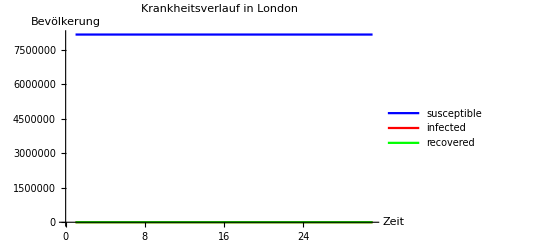

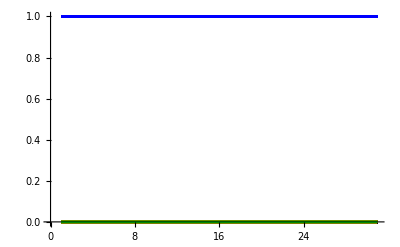

```mathematica
doTimestep["London",0,30,"NDS"]
plot["London"]
plotAll
```

Wie erwartet bleibt die gesamte Bevölkerung in der Gruppe der susceptibles und es gibt keine Personen in den infected- und recovered-Gruppen

Können Sie anhand der Differenzialgleichungen Grenzfälle für bestimmte Parameter erkennen? Können Sie diese in Ihrem Modell bestätigen?

Mit der Größe 1/ν kann man die Krankheitsdauer identifizieren, was bei dem vorgegebenen Parameter ν = 0.07 einer Krankheitsdauer von etwa 14 Tagen entspricht.
Multipliziert man nun β mit der Krankheitsdauer 1/ν so erhält man die Anzahl von Personen, die jeder Infizierte während seiner Krankheit anstecken kann.
Ist β/ν  > 1, so kann jeder Infizierte mehrere gesunde Personen anstecken und die Krankheit wird zur Epidemie.
Ist β/ν ≤ 1, so wird die Krankheit schnell aussterben, da es wahrscheinlicher ist, dass ein Infizierter während seiner Krankheitsdauer keine weiteren Personen ansteckt.

Im Beispiel der Aufgabenstellung mit β = 0.1 und ν = 0.07 ist der Quotient größer als 1, also wird sich die Krankheit ausbreiten.

Simulation der Krankheit mit β = 0.1, ν = 0.07, μ = 3*10^-5, pt = 0.01 und 1000 Infizierten in London für 30 Zeitschritte:

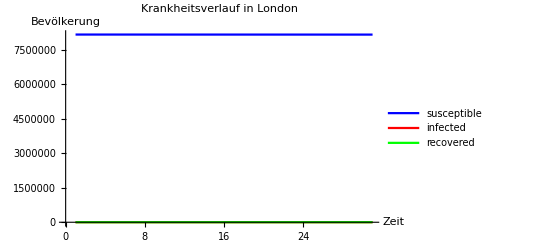

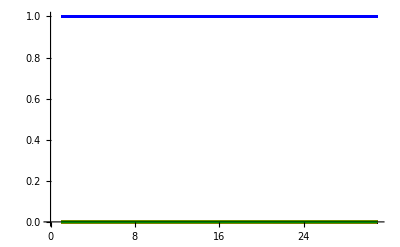

```mathematica
doTimestep["London",1000,30,"NDS"]
plot["London"]
plotAll
```

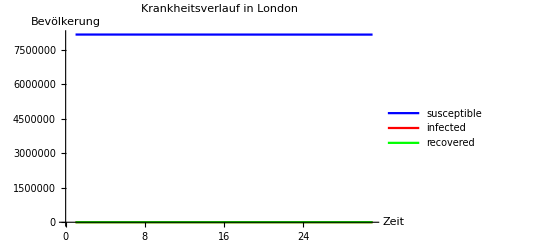

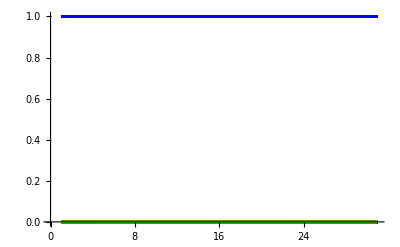

```mathematica
doTimestep["London",1000,30,"Eul"]
plot["London"]
plotAll
```

```mathematica
doTimestep["London",1000,30,"RK4"]
plot["London"]
plotAll
```

-Graphics-

-Graphics-

Man erkennt, dass bei den gegebenen Parametern innerhalb von 30 Tagen keine Veränderung der susceptible, infected und recovered Gruppen stattgefunden hat. Dies liegt daran, dass die Infektionsrate β klein ist und somit über einen kurzen Zeitraum nicht genug Personen infiziert werden können. Anhand dieses Tests kann man auch noch keinen Unterschied zwischen den verschiedenen Lösungsmethoden feststellen.

Um eine Veränderung der SIR-Gruppen zu sehen, muss man entweder den Krankheitsparameter β erhöhen, oder weitaus mehr Zeitschritte durchführen. 

Um Rechenzeit zu sparen, haben wir die Simulation zuvor mit den vorgegebenen Parametern für 1500 Zeitschritte durchgeführt und den Plot für London Exportiert. Dieser wird nun importiert und angezeigt:

```mathematica
timestep1500=Import["doTimeStep_London_1000_1500_RK4.pdf"];
Show[timestep1500,Label->"sbfio"]
```

-Graphics-

In diesem Plot wird deutlich, dass der Peak der Infektionskurve (gelb) einen nur kleinen Wert erreicht und die Krankheit nach ca. 600 Tagen ausgerottet ist.
Da das Ausführen so vieler Zeitschritte jedoch viel Rechenzeit benötigt, wird im folgenden der Parameter β variiert.

Im Folgenden wird β auf 0.5 gesetzt und die Entwicklung der Krankheit über 110 Tage beobachtet. Außerdem wird zum Vergleich der Lösungsmethoden die Zeit der Simulation mit der Funktion Timing gemessen.

```mathematica
Clear[beta];
beta=0.5;
```

{137.906,Null}

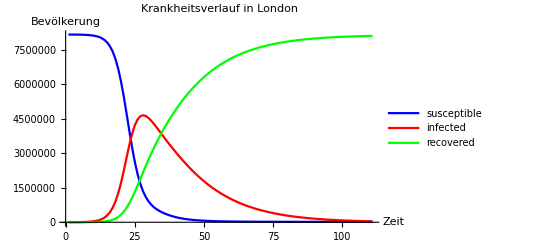

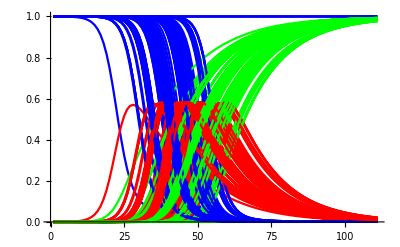

```mathematica
doTimestep["London",1000,110,"NDS"]//Timing
plot["London"]
plotAll
```

{69.2031,Null}

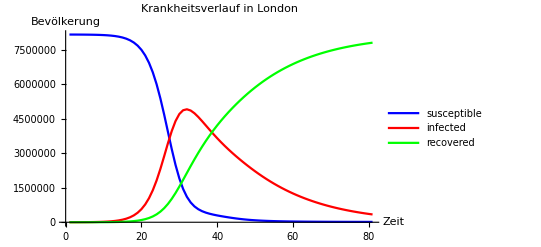

-Graphics-

```mathematica
doTimestep["London",1000,80,"Eul"]//Timing
plot["London"]
plotAll
```

```mathematica
doTimestep["London",1000,80,"RK4"]//Timing
plot["London"]
plotAll
```

{59.7656,Null}

-Graphics-

-Graphics-

Man erkennt, dass NDSolve bei Weitem das langsamste Lösungsverfahren ist, aber womöglich die genauesten Ergebnisse liefert. Bei den beiden anderen Verfahren (vor allem beim Euler-Verfahren) sieht man, dass die Kurven nach rechts verschoben sind, was auf die Fehler der Euler- und Runge-Kutta-Verfahren zurückzuführen ist. Diese Fehler wachsen mit der Änderung der Steigung, weshalb der Fehler bei großem β auch größer wird. Um diese Fehler einzudämmen könnte z.B. die Schrittweite des Euler-Verfahrens verkleinern, was jedoch durch längere Rechenzeiten bestraft wird.
Im Endeffekt muss man seine Lösungsmethode also an die Parameter der Krankheit und die zu Verfügung stehende Rechenzeit/-leistung anpassen.


Da mit den neuen Parametern eine anschaulichere (wenn auch nicht unbedingt realistischere) Krankheit simuliert wird, kann man nun erneut eine Animation mit der Funktion “animateEurope” starten. Dazu werden zunächst 100 Zeitschritte mit der Lösungsmethode RK4 durchgeführt, da diese am schnellsten ist.

```mathematica
doTimestep["London",1000,100,"RK4"]
animateEurope
```

In der Animation ist nach etwa 20 Schritten erkennbar, dass sich der Punkt in London rot verfärbt, was bedeutet, dass der Anteil an Infizierten dort steigt. Nach 30 Zeitschritten beginnen sich die Punkte der großen Städte mit Flughafen (Paris, Madrid, Kiev, Berlin, Rom) rot zu färben, da dort die infizierten Personen mit dem Flugzeug ankommen. Ab dem 30. Zeitschritt kann man erkennen, dass sich die Krankheit ausgehend von diesen Städten in Form einer roten Welle über die Landverbindungen auszubreiten beginnt, bis fast ganz Europa einmal infiziert war. Der roten Welle an Infizierten folgt jedoch schnell eine grüne Welle, die das Genesen der Bevölkerung darstellt, bis ganz Europa grün eingefärbt und die Krankheit somit überstanden ist.
Dieses Verhalten der jeweiligen Bevölkerungsgruppe spiegelt sich auch in den oben erzeugten Plots wieder, wo man erkennen kann, dass verschiedene Städte ihren Infektionspeak zu verschiedenen Zeitpunkten erreichen.

## Erweiterung des Netzwerkes auf Europa und Nordamerika

### Im Folgenden erweitern wir unser Modell auf Nordamerika. Diese Implementation wird dadurch realisiert, dass alle Flughäfen Nordamerikas und Europas verbunden werden und somit der Reiseverkehr zwischen den beiden Kontinenten ermöglicht wird. Die Erstellung der Listen erfolgte völlig analog zu Europa und wird hier nicht erneut dargestellt. Die entsprechenden Listen sind mit einem “NA” am Ende gekennzeichnet und müssen lediglich importiert werden.

## Import der Daten für Nordamerika:

### Analoge Erstellung der Listen für Nordamerika ergibt die folgenden Listen:

```mathematica
SetDirectory[NotebookDirectory[]];
bigcitiesNA=ToExpression[Import["bigcitiesNA.txt"]];
bigcitynamesNA=Import["bigcitynamesNA.txt","Data"];
citiesNA=ToExpression[Import["citiesNA.txt"]];
popNA=Normal[ToExpression[Import["popNA.txt"]]];
citynamesNA=Import["citynamesNA.txt","Data"];
landnamesNA=ToExpression[Import["landnamesNA.txt","Data"]];
airnamesNA=ToExpression[Import["airnamesNA.txt","Data"][[1]]];
```

## Modifikation der grundlegenden Funktionen für Nordamerika:

### Alle grundlegenden Funktionen von Europa können nun auf das größere Netzwerk erweitert werden, indem ihnen die “globalen” Listen übergeben werden.

```mathematica
indexAirGlobal[city_String]:=Position[bigcitynamesGlobal,city][[1,1]];
indexGlobal[city_]:=Position[citynamesGlobal,city][[1,1]];
infectGlobal[city_,inf0_]:=Module[{j,inf1,landinf1},
j=indexGlobal[city];

inf1={Table[If[j==i,inf0,0],{i,Length[citynamesGlobal]}]};     

sus={popGlobal}-inf1;

inf=inf1;

rec={Table[0,Length[citynamesGlobal]]};
]
```

## Modifikation der bestehenden Listen für das größere Netzwerk:

### Um das Netzwerk zu erweitern, müssen lediglich die oben für Nordamerika erstellten Listen mit den entsprechenden Listen für Europa zusammengeführt werden:

```mathematica
bigcitiesGlobal=Join[bigcities,bigcitiesNA];
bigcitynamesGlobal=Join[bigcitynames,bigcitynamesNA];
airnamesGlobal=Complement[bigcitynamesGlobal,{#}]&/@bigcitynamesGlobal;
indexAirListGlobal=ToExpression[Import["indexAirListGlobal.txt","List"]];
citynamesGlobal=Join[citynames,citynamesNA];
landnamesGlobal=Join[landnames,landnamesNA];
indexLandListGlobal=Map[indexGlobal[#]&,landnamesGlobal,{2}];
popGlobal=Join[pop,popNA];
citiesGlobal=Join[cities,citiesNA];
citiesPosGolbal=Map[EntityValue[#,"Position"]&,citiesGlobal,{1}];
```

## Modifikation der Reise- und Infect-Funktionen:

### Auch die Reise- und Infect-Funktionen können aus dem europäischen Modell übernommen werden, wenn ihnen die neuen Listen übergeben werden. In diesem erweiterten Modell beschränken wir uns für die Lösungsmethode der Differentialgleichungen des SIR-Modells auf die Runge-Kutta-Methode, da diese am schnellsten arbeitet.

```mathematica
travelAirGlobal[city_]:=If[MemberQ[bigcitynamesGlobal,city],Module[{j,i,listDest,popChange,s0,i0,r0,popNew},
j=indexGlobal[city];
i=indexAirGlobal[city];

listDest=indexAirListGlobal[[i]];

popChange=travelCalc[listDest];

s0=Last[sus][[j]];
i0=Last[inf][[j]];
r0=Last[rec][[j]];

popNew=
{s0+popChange/.{p0->s0,pN[k_]:>Last[sus][[k]]},
i0+popChange/.{p0->i0,pN[k_]:>Last[inf][[k]]},
r0+popChange/.{p0->r0,pN[k_]:>Last[rec][[k]]}}
/.{pop0->s0+i0+r0,popN[k_]:>Last[sus][[k]]+Last[inf][[k]]+Last[rec][[k]],pt->ptair};

Return[popNew]
],{Last[sus][[indexGlobal[city]]],Last[inf][[indexGlobal[city]]],Last[rec][[indexGlobal[city]]]}]

travelAirAllGlobal:=Module[{susN,infN,recN},
susN=Map[travelAirGlobal[#][[1]]&,citynamesGlobal,{1}];
infN=Map[travelAirGlobal[#][[2]]&,citynamesGlobal,{1}];
recN=Map[travelAirGlobal[#][[3]]&,citynamesGlobal,{1}];
AppendTo[sus,susN];
AppendTo[inf,infN];
AppendTo[rec,recN];
]

travelLandGlobal[city_]:=Module[{j,listDest,popChange,s0,i0,r0,popNew},
j=indexGlobal[city];
listDest=indexLandListGlobal[[j]];

popChange=travelCalc[listDest];

s0=Last[sus][[j]];
i0=Last[inf][[j]];
r0=Last[rec][[j]];

popNew=
{s0+popChange/.{p0->s0,pN[k_]:>Last[sus][[k]]},
i0+popChange/.{p0->i0,pN[k_]:>Last[inf][[k]]},
r0+popChange/.{p0->r0,pN[k_]:>Last[rec][[k]]}}
/.{pop0->s0+i0+r0,popN[k_]:>Last[sus][[k]]+Last[inf][[k]]+Last[rec][[k]],pt->ptland};
Return[popNew]
]

travelLandAllGlobal:=Module[{susN,infN,recN},
susN=Map[travelLandGlobal[#][[1]]&,citynamesGlobal,{1}];
infN=Map[travelLandGlobal[#][[2]]&,citynamesGlobal,{1}];       
recN=Map[travelLandGlobal[#][[3]]&,citynamesGlobal,{1}];

AppendTo[sus,susN];
AppendTo[inf,infN];      
AppendTo[rec,recN];
]

infectRK4Global[city_] := Module[{j, i0, s0, r0, p0, sys, s, i, r, K1, K2, K3, K4, t, sol},
  j = indexGlobal[city];
  
  p0 = popGlobal[[j]];
  i0 = Last[inf][[j]];
  s0 = Last[sus][[j]];   
  r0 = Last[rec][[j]];
  
  sys = {s'[t] == mu*p0 - beta*s[t]*i[t]/p0 - mu*s[t],    
    i'[t] == beta*s[t]*i[t]/p0 - nu*i[t] - mu*i[t],
    r'[t] == nu*i[t] - mu*r[t]};
  
  K1[y_] := K1[y] = sys[[y, 2]] /. {s[t] -> s0, i[t] -> i0, r[t] -> r0};
  K2[y_] := K2[y] = sys[[y, 2]] /. {s[t] -> s0 + K1[1]/2, i[t] -> i0 + K1[2]/2, r[t] -> r0 + K1[3]/2};
  K3[y_] := K3[y] = sys[[y, 2]] /. {s[t] -> s0 + K2[1]/2, i[t] -> i0 + K2[2]/2, r[t] -> r0 + K2[3]/2};             
  K4[y_] := K4[y] = sys[[y, 2]] /. {s[t] -> s0 + K3[1], i[t] -> i0 + K3[2], r[t] -> r0 + K3[3]};
  
  sol = {s0 + 1/6 (K1[1] + 2 K2[1] + 2 K3[1] + K4[1]),
    i0 + 1/6 (K1[2] + 2 K2[2] + 2 K3[2] + K4[2]),
    r0 + 1/6 (K1[3] + 2 K2[3] + 2 K3[3] + K4[3])};
  Return[sol]
  ]

infectRK4AllGlobal:=Module[{susN,infN,recN,susO,infO,recO,landsusN,landinfN,landrecN,landpopN},
susN=Table[infectRK4Global[citynamesGlobal[[i]]][[1]],{i,1,Length[citynamesGlobal]}];
infN=Table[infectRK4Global[citynamesGlobal[[i]]][[2]],{i,1,Length[citynamesGlobal]}];
recN=Table[infectRK4Global[citynamesGlobal[[i]]][[3]],{i,1,Length[citynamesGlobal]}];
AppendTo[sus,susN];
AppendTo[inf,infN];
AppendTo[rec,recN];
]
```

## Modifikation der Funktion zum Ausführen der Zeitschritte:

### Die Funktionen zum Ausführen der Zeitschritte funktionieren ebenfalls analog zu denen aus dem europäischen Modell. Lediglich die Switch-Funktion zum Auswählen der Lösungsmethode ist nun überflüssig und wurde entfernt, weshalb dem Modul auch nun nur noch 3 Parameter übergeben werden müssen.

```mathematica
doTimestepGlobal[city_,inf0_,t_]:=Module[{},
infectGlobal[city,inf0];

Do[
travelLandAllGlobal;
travelAirAllGlobal;
infectRK4AllGlobal,t]
]

continueTimestepGlobal[t_]:=Module[{},
Do[
travelLandAllGlobal;
travelAirAllGlobal;
infectRK4AllGlobal,t]
]
```

## Modifikation der Funktion zum Erstellen der Animation für Nordamerika und Europa:

```mathematica
animateGlobal:=Module[{table},
Clear[geotable];
table=Table[Table[{PointSize[1/125],RGBColor[inf[[t,j]]/popGlobal[[j]],rec[[t,j]]/popGlobal[[j]],sus[[t,j]]/popGlobal[[j]]],Point[citiesPosGolbal[[j]]]},{j,Length[citiesGlobal]}],{t,1,Length[sus],3}];
geotable=Table[GeoGraphics[table[[j]],ImageSize->Large],{j,1,Length[table]}];
Manipulate[geotable[[j]],{{j,1,"Tage"},1,Length[geotable],1,Appearance->"Open"},FrameLabel->{Blue->"susceptible" Red->"infected" Green->"recovered"}]
]
```

## Test der Implementation auf dem großen Netzwerk

### Um das erweiterte Modell zu testen, starten wir erneut eine Simulation mit 1000 Infizierten in London und lassen uns die Animation ausgeben:

```mathematica
Clear[beta];
beta=0.5;
doTimestepGlobal["London",1000,100]
animateGlobal
```

Auch in diesem Modell sind nach 30 Tagen zuerst die Großstädte mit Flughafen infiziert. Von den Großstädten ausgehend breitet sich dann, in Nordamerika wie in Europa, die Krankheit über die Landwege aus. In Nordamerika fällt allerdings auf, dass einige Städte, vor allem im Norden, gar nicht infiziert werden. Dies ist der Fall, da diese Städte keinen Flughafen besitzen und über 500 Kilometer von ihren nächsten Nachbarn entfernt sind, was mit unserem Reisemodell keine Infektion (außer direkt durch Start der Epidemie dort) möglich macht.

## Weiterführende Untersuchungen und Modifikationen:

## Reiseparameter abhängig vom Gesundheitszustand

### Da es in der Realität meist der Fall ist, dass erkrankte Personen weniger gewillt sind, eine Reise anzutreten, oder erst gar nicht das Haus verlassen, werden im Folgenden die Reise-Funktionen so modifiziert, dass die infizierte Bevölkerung weniger reist als die Gesunde. Unsere Annahme für dieses Modell war, dass sich die Reiserate für infizierte Personen auf ein Zwanzigstel des ursprünglichen Wertes für gesunde Personen verringert.

```mathematica
travelLandVariable[city_]:=Module[{j,listDest,popChange,s0,i0,r0,popNew},
j=index[city];
listDest=indexLandList[[j]];

popChange=travelCalc[listDest];

s0=Last[sus][[j]];
i0=Last[inf][[j]];
r0=Last[rec][[j]];

popNew=
{s0+popChange/.{p0->s0,pN[k_]:>Last[sus][[k]],pt->ptland},
i0+popChange/.{p0->i0,pN[k_]:>Last[inf][[k]],pt->ptland*0.05},
r0+popChange/.{p0->r0,pN[k_]:>Last[rec][[k]],pt->ptland}}
/.{pop0->s0+i0+r0,popN[k_]:>Last[sus][[k]]+Last[inf][[k]]+Last[rec][[k]]};
(*Hier wird der Parameter pt nicht für alle Bevölkerungsgruppen gleichzeitig ersetzt, sondern für jede einzeln. Dabei wird er Wert nur bei der Gruppe inf auf ein Zwanzigstel des Ursprungwertes reduziert.*)
Return[popNew]
]
```

```mathematica
travelLandAllVariable:=Module[{susN,infN,recN},
susN=Map[travelLandVariable[#][[1]]&,citynames,{1}];
infN=Map[travelLandVariable[#][[2]]&,citynames,{1}];       (*Anwenden der modifizierten Travel-Funktionen auf jede Stadt*)
recN=Map[travelLandVariable[#][[3]]&,citynames,{1}];

AppendTo[sus,susN];
AppendTo[inf,infN];      
AppendTo[rec,recN];
]
```

```mathematica
travelAirVariable[city_]:=If[MemberQ[bigcitynames,city],Module[{j,i,listDest,popChange,s0,i0,r0,popNew},
j=index[city];
i=indexAir[city];

listDest=indexAirList[[i]];

popChange=travelCalc[listDest];

s0=Last[sus][[j]];
i0=Last[inf][[j]];
r0=Last[rec][[j]];

popNew=
{s0+popChange/.{p0->s0,pN[k_]:>Last[sus][[k]],pt->ptair},
i0+popChange/.{p0->i0,pN[k_]:>Last[inf][[k]],pt->ptair*0.05},
r0+popChange/.{p0->r0,pN[k_]:>Last[rec][[k]],pt->ptair}}
/.{pop0->s0+i0+r0,popN[k_]:>Last[sus][[k]]+Last[inf][[k]]+Last[rec][[k]]};
(*Auch hier wird, wie in der travelLandVariable-Funktion nur der Reiseparameter der Gruppe inf mit 0.05 multipliziert*)
Return[popNew]
],{Last[sus][[index[city]]],Last[inf][[index[city]]],Last[rec][[index[city]]]}]
```

```mathematica
travelAirAllVariable:=Module[{susN,infN,recN},
susN=Map[travelAirVariable[#][[1]]&,citynames,{1}];
infN=Map[travelAirVariable[#][[2]]&,citynames,{1}];       (*Anwenden der modifizierten Travel-Funktionen auf jede Stadt*)
recN=Map[travelAirVariable[#][[3]]&,citynames,{1}];
AppendTo[sus,susN];
AppendTo[inf,infN];
AppendTo[rec,recN];
]
```

```mathematica
doTimestepVariable[city_,inf0_,t_,Method_]:=Module[{func},
infect[city,inf0];

func:=Switch[Method,"RK4",infectRK4All,"Eul",infectEulAll,"NDS",infectNDSAll];
Do[
travelLandAllVariable;
travelAirAllVariable;
func,t]
]
```

```mathematica
continueTimestepVariable[t_,Method_]:=Module[{func},

func:=Switch[Method,"RK4",infectRK4All,"Eul",infectEulAll,"NDS",infectNDSAll];
Do[
travelLandAllVariable;
travelAirAllVariable;
func,t]
]
```

### Zum Test des gesundheitsabhängigen Reisemodells starten wir erneut eine Simulation über 100 Zeitschritte mit 1000 Infizierten in London:

```mathematica
Clear[beta];
beta=0.5;
doTimestepVariable["London",1000,100,"RK4"]
animateEurope
plotAll
```

Es ist erkennbar, dass die räumliche Ausbreitung der Krankheit langsamer fortschreitet als im ursprünglichen Modell. Nach 80 Zeitschritten waren in diesem bereits alle Städte grün, wohingegen im modifizierten Modell zu diesem Zeitpunkt noch einige Städte rot erscheinen. Außerdem ist in dem unteren Plot sehr gut zu erkennen, dass die Infektionspeaks teilweise erst sehr spät eintreten und die Kurven generell weiter auseinander liegen.

## Flughafenschließungen

### Eine Möglichkeit, die Ausbreitung einer solchen Epidemie zu verhindern oder einzuschränken ist es, die Flughäfen zu schließen. Dafür wird die Funktion zum Ausführen der Zeitschritte so modifiziert, dass Flugreisen nach einer vorher an die Funktion zu übergebenden Zeitspanne “tClose_” nicht mehr möglich sind.

```mathematica
doTimestepGlobalClosing[city_,inf0_,t_,tClose_]:=Module[{},
infectGlobal[city,inf0];


Do[
travelLandAllGlobal;
If[t≤tClose,travelAirAllGlobal,
AppendTo[sus,Last[sus]];
AppendTo[inf,Last[inf]];
AppendTo[rec,Last[rec]]]; (*Durch diese If-Abfrage werden Flugreisen nach tClose_ Tagen nicht mehr durchgeführt und es wird der vorherige Wert der jeweiligen Liste angehängt.*)
infectRK4AllGlobal,t]
]
```

### Zum Test dieser Gegenmaßnahme Starten wir eine globale Simulation mit 1000 Infizierten in London, die für 150 Tage läuft, aber bereits nach 5 Tagen die Flugreisen sperrt.

```mathematica
Clear[beta];
beta=0.5;
doTimestepGlobalClosing["London",1000,150,5]
animateGlobal
```

Hier fällt auf, dass zu Beginn noch Flugreisen stattfinden, da Nordamerika sonst nicht infiziert worden wäre. Jedoch ist erkennbar dass die Ausbreitung der Krankheit nur über Landreisen stattfindet, da sich die “rote Welle” nur von einem Punkt ausgehend ausbreitet und nicht von mehreren Großstädten (beispielsweise wird Osteuropa erst weitaus später infiziert als in der ursprünglichen Simulation, da Kiew nicht als Ausgangspunkt dient).

## Zeitabhängiger Krankheitsparameter

In der letzten Implementierung wird β zeitlich variiert, um dadurch saisonale Schwankungen des Krankheitsparameters zu erhalten.  Deswegen wird β mit β*(Sin[2*Pi*(Length[sus]-1)/365]+1) ersetzt, was zu Folge hat, dass β niemals negativ wird und zu Beginn ansteigt, was man mit dem Herbst assoziieren könnte, da es auf den Winter zugeht, bei dem β sein Maximum erreicht. Da sich im Winter leichter Krankheiten ausbreiten aufgrund der Schwächung des Immunsystems. 
Außerdem beschreibt eine ganze Periode des Sinus ein ganzes Jahr.

### Funktionen zum Ausführen von Zeitschritten und Infect-Funktion

```mathematica
doTimestepSeason[city_,inf0_,t_]:=Module[{func},
infect[city,inf0];

Do[
travelLandAll;
travelAirAll;
infectNDSAllSeason,t]
]
```

```mathematica
infectNDSSeason[city_,season_]:=Module[{j,sys,s,i,r,p,t,sN,iN,rN,sol,p0,i0,s0,r0},
j=index[city];

p0=pop[[j]];
i0=Last[inf][[j]];
s0=Last[sus][[j]];     
r0=Last[rec][[j]];

sys={                         
s'[t]==mu*p0-beta*(Sin[2*Pi*(Length[sus]-1)/365]+1)*s[t]*i[t]/p0-mu*s[t],        
i'[t]==beta*(Sin[2*Pi*(Length[sus]-1)/365]+1)*s[t]*i[t]/p0-nu*i[t]-mu*i[t],
r'[t]==nu*i[t]-mu*r[t],

i[0]==i0,
s[0]==s0,      
r[0]==r0
};
sol=NDSolve[sys,{s[t],i[t],r[t]},{t,0,1}];     
sN[t]=s[t]/.sol;
iN[t]=i[t]/.sol;             
rN[t]=r[t]/.sol;

Return[Flatten[{sN[t],iN[t],rN[t]}/.t->1]]          
]
```

```mathematica
infectNDSAllSeason:=Module[{susN,infN,recN,susO,infO,recO,landsusN,landinfN,landrecN,landpopN},
susN=Table[infectNDSSeason[citynames[[i]]][[1]],{i,1,Length[cities]}];
infN=Table[infectNDSSeason[citynames[[i]]][[2]],{i,1,Length[cities]}];          
recN=Table[infectNDSSeason[citynames[[i]]][[3]],{i,1,Length[cities]}];
AppendTo[sus,susN];
AppendTo[inf,infN];
AppendTo[rec,recN];
]
```

### Test der Implementierung für Saisonale Veränderung

```mathematica
Clear[beta];
beta=0.5;
doTimestepSeason["London",1000,100]
plot["London"]
plotAll
```

-Graphics-

-Graphics-

Wenn man diese Plot mit den ursprünglichen Plots vergleicht,  nehmen die infizierten Personen wesentlich früher ihr Maximum an, was damit zu erklären ist, dass die Sinus Funktion zuerst ansteigt und dadurch zu Beginn β ebenfalls ansteigt. Die Kurve der Infizierten beginnt also früher zu steigen, steigt wesentlich stärker und nimmt einen höheren Maximalwert an, als im ursprünglichen Modell.